# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z)+C sin^(2k)(z))(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1

Domain Map

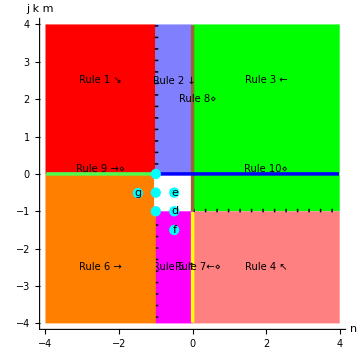

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z)+C sin^(2k)(z))ⅆz when j^2=1∧k^2=1

Rules 7-8:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))ⅆx

#### Derivation: Rule 7b with B=0 and A+(A+C)(m+(k+1)/2)=0

#### Rule 7a: If j^2=k^2=1 ∧ A+(A+C)(j k m+(k+1)/2)=0, then

∫(Sin[c+d x]^j)^m(A+C Sin[c+d x]^(2k))ⅆx  ⟶  (A Cos[c+d x](Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2))

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+C_.*sin[c_.+d_.*x_]^k2_),x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k2/2)/(d*(j*k2/2*m+(k2/2+1)/2)) /;
FreeQ[{c,d,A,C,m},x] && OneQ[j^2,k2^2/4] && ZeroQ[A+(A+C)*(j*k2/2*m+(k2/2+1)/2)]
```

#### Derivation: Rule 5 with a=1, b=0 and n=0

#### Rule 7b: If j^2=k^2=1 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 , then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))ⅆx  ⟶  (A Cos[c+d x](Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2))+
1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k) (B(j k m+(k+1)/2)+(A+(A+C)(j k m+(k+1)/2))Sin[c+d x]^k )ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_),x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*Sim[B*(j*k*m+(k+1)/2)+(A+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x],x]] /;
FreeQ[{c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && RationalQ[m] && j*k*m+(k+1)/2≠0 && j*k*m≤-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_+C_.*sin[c_.+d_.*x_]^k2_),x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k2/2)/(d*(j*k2/2*m+(k2/2+1)/2)) + 
  Dist[(A+(A+C)*(j*k2/2*m+(k2/2+1)/2))/(j*k2/2*m+(k2/2+1)/2),Int[(sin[c+d*x]^j)^(m+j*k2),x]] /;
FreeQ[{c,d,A,C},x] && OneQ[j^2,k2^2/4] && RationalQ[m] && j*k2/2*m+(k2/2+1)/2≠0 && j*k2/2*m≤-1
```

#### Derivation: Rule 2 with a=0, b=1 and n=0

#### Rule 8: If j^2=k^2=1 ∧ j k m+(k+3)/2≠0 ∧ j k m≥-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))ⅆx  ⟶  -(C Cos[c+d x](Sin[c+d x]^j)^(m+j k))/(d (j k m+(k+3)/2))+
1/(j k m+(k+3)/2)∫(Sin[c+d x]^j)^m (A+(A+C)(j k m+(k+1)/2)+B(j k m+(k+3)/2)Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_),x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+3)/2)) + 
  Dist[1/(j*k*m+(k+3)/2),
    Int[(sin[c+d*x]^j)^m*Sim[A+(A+C)*(j*k*m+(k+1)/2)+B*(j*k*m+(k+3)/2)*sin[c+d*x]^k,x],x]] /;
FreeQ[{c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && RationalQ[m] && j*k*m+(k+3)/2≠0 && j*k*m≥-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_+C_.*sin[c_.+d_.*x_]^k2_),x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k2/2)/(d*(j*k2/2*m+(k2/2+3)/2)) + 
  Dist[(A+(A+C)*(j*k2/2*m+(k2/2+1)/2))/(j*k2/2*m+(k2/2+3)/2),Int[(sin[c+d*x]^j)^m,x]] /;
FreeQ[{c,d,A,C},x] && OneQ[j^2,k2^2/4] && RationalQ[m] && j*k2/2*m+(k2/2+3)/2≠0 && j*k2/2*m≥-1
```

# Integration Rules for ∫(A+B sin^k(z)+C sin^(2k)(z))(a+b sin^k(z))^n ⅆz when k^2=1

Rule a:  ∫(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))/(a+b Sin[c+d x]^k)ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z+C z^2)/(a+b z)=(C z)/b+(b A+(b B-a C)z)/(b(a+b z))

#### Rule a1:

∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(a+b Sin[c+d x])ⅆx  ⟶  -(C Cos[c+d x])/(b d)+1/b∫(b A+(b B-a C)Sin[c+d x])/(a+b Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  -C*Cos[c+d*x]/(b*d) + Dist[1/b,Int[(b*A+(b*B-a*C)*sin[c+d*x])/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B,C},x]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^2)/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  -C*Cos[c+d*x]/(b*d) + Dist[1/b,Int[(b*A-a*C*sin[c+d*x])/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,C},x]
```

#### Derivation: Algebraic expansion

#### Basis: (A+B z^-1+C z^-2)/(a+b z^-1)=A/a+(a C-(b A-a B) z)/(a z (b+a z))

#### Rule a2: If a^2-b^2≠0, then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2)/(a+b Csc[c+d x])ⅆx  ⟶  (A x)/a+∫(C+(B-b A/a)Sin[c+d x])/(Sin[c+d x](b+a Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  A*x/a + Int[(C+(B-b*A/a)*sin[c+d*x])/(sin[c+d*x]*(b+a*sin[c+d*x])),x] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^(-2))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  A*x/a + Int[(C-b*A/a*sin[c+d*x])/(sin[c+d*x]*(b+a*sin[c+d*x])),x] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

∫(A+B Csc[c+d x]+C Csc[c+d x]^2) (a+b Csc[c+d x])^(n/2)ⅆx

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√z √(1/z))=0

#### Rule: If n^2=1, then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2)(b Csc[c+d x])^(n/2)ⅆx  ⟶
(Sin[c+d x])^(n/2)(b Csc[c+d x])^(n/2)∫(C+B Sin[c+d x]+A Sin[c+d x]^2)/Sin[c+d x]^(n/2+2)ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))*(b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sin[c+d*x]^n*(b*Csc[c+d*x])^n,Int[(C+B*sin[c+d*x]+A*sin[c+d*x]^2)/sin[c+d*x]^(n+2),x]] /;
FreeQ[{b,c,d,A,B,C},x] && ZeroQ[n^2-1/4]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^(-2))*(b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sin[c+d*x]^n*(b*Csc[c+d*x])^n,Int[(C+A*sin[c+d*x]^2)/sin[c+d*x]^(n+2),x]] /;
FreeQ[{b,c,d,A,C},x] && ZeroQ[n^2-1/4]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√(b+a f[z]))/(√f[z]√(a+b/f[z]))=0

#### Rule: If a^2-b^2≠0 ∧ n-1/2∈ℤ ∧ -2<n<0, then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2)(a+b Csc[c+d x])^n ⅆx  ⟶  
(√(b+a Sin[c+d x]))/(√Sin[c+d x]√(a+b Csc[c+d x]))∫((C+B Sin[c+d x]+A Sin[c+d x]^2)(b+a Sin[c+d x])^n)/Sin[c+d x]^(n+2)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_+d_.*x_]^(-2))*(a_.+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[(C+B*sin[c+d*x]+A*sin[c+d*x]^2)*(b+a*sin[c+d*x])^n/sin[c+d*x]^(n+2),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && IntegerQ[n-1/2] && -2<n<0
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[(C+A*sin[c+d*x]^2)*(b+a*sin[c+d*x])^n/sin[c+d*x]^(n+2),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && IntegerQ[n-1/2] && -2<n<0
```

∫(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Algebraic simplification

#### Basis: If a^2 C-a b B+b^2 A=0, then A+B z+C z^2=1/b^2(b B-a C+b C z)(a+b z)

#### Rule: If k^2=1 ∧ a^2 C-a b B+b^2 A=0 ∧ n<-1, then

∫(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
1/b^2∫(b B-a C+b C Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[1/b^2,Int[Sim[b*B-a*C+b*C*sin[c+d*x]^k,x]*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[k^2] && k2===2*k && ZeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && 
  n<-1
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  Dist[C/b^2,Int[Sim[-a+b*sin[c+d*x]^k,x]*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[k^2] && k2===2*k && ZeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1
```

Rules 17-18:  ∫(A+B Csc[c+d x]+C Csc[c+d x]^2) (a+b Csc[c+d x])^n ⅆx

#### Derivation: Rule 6 with m=0 and k=-1

#### Rule 17: If a^2-b^2≠0 ∧ a^2 C-a b B+b^2 A≠0 ∧ n<-1, then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2) (a+b Csc[c+d x])^n ⅆx  ⟶  
((a^2 C-a b B+b^2 A) Cot[c+d x](a+b Csc[c+d x])^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))·
 ∫(A (a^2-b^2) (n+1)-a(b A-a B+b C)(n+1)Csc[c+d x]+(a^2 C-a b B+b^2 A)(n+2)Csc[c+d x]^2)(a+b Csc[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  (a^2*C-a*b*B+b^2*A)*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[Sim[A*(a^2-b^2)*(n+1)-(a*(b*A-a*B+b*C)*(n+1))*sin[c+d*x]^(-1)+
        (a^2*C-a*b*B+b^2*A)*(n+2)*sin[c+d*x]^(-2),x]*
      (a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && n<-1
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  (a^2*C+b^2*A)*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[Sim[A*(a^2-b^2)*(n+1)-(a*b*(A+C)*(n+1))*sin[c+d*x]^(-1)+(a^2*C+b^2*A)*(n+2)*sin[c+d*x]^(-2),x]*
      (a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1
```

#### Derivation: Rule 3 with m=0 and k=-1

#### Note: If A=B=a^2-b^2=0, there is an a^2-b^2=0 rule that simplifies resulting integrand to (a+b Csc[c+d x])^n.

#### Rule 18: If n>0 ∧ ¬(A=B=a^2-b^2=0), then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2) (a+b Csc[c+d x])^n ⅆx  ⟶  
-(C Cot[c+d x](a+b Csc[c+d x])^n)/(d (n+1))+1/(n+1)·
∫(a A(n+1)+(b A+a B+n(b A+a B+b C))Csc[c+d x]+(a C n+b B (n+1))Csc[c+d x]^2)(a+b Csc[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -C*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(n+1)) + 
  Dist[1/(n+1),
    Int[Sim[a*A*(n+1)+(b*A+a*B+n*(b*A+a*B+b*C))*sin[c+d*x]^(-1)+(a*C*n+b*B*(n+1))*sin[c+d*x]^(-2),x]*
      (a+b*sin[c+d*x]^(-1))^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && RationalQ[n] && n>0
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -C*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(n+1)) + 
  Dist[1/(n+1),
    Int[Sim[a*A*(n+1)+b*(A+n*(A+C))*sin[c+d*x]^(-1)+a*C*n*sin[c+d*x]^(-2),x]*
      (a+b*sin[c+d*x]^(-1))^(n-1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && RationalQ[n] && n>0 && Not[ZeroQ[A] && ZeroQ[a^2-b^2]]
```

Rules 15-16:  ∫(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (b Sin[c+d x]^k)^n ⅆx

#### Derivation: For k=1, Rule 9b with k=1

#### Derivation: For k=-1, ???

#### Rule 15: If k^2=1 ∧ n<-1, then

∫(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(b Sin[c+d x]^k)^n ⅆx  ⟶  (2A Cos[c+d x](b Sin[c+d x]^k)^(n+1))/(b d (2n+k+1))+
1/(b (2n+k+1))∫((2n+k+1) B+(2A+(A+ C)(2n+k+1)) Sin[c+d x]^k)(b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  2*A*Cos[c+d*x]*(b*Sin[c+d*x]^k)^(n+1)/(b*d*(2*n+k+1)) + 
  Dist[1/(b*(2*n+k+1)),
    Int[Sim[(2*n+k+1)*B+(2*A+(A+C)*(2*n+k+1))*sin[c+d*x]^k,x]*(b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{b,c,d,A,B,C},x] && OneQ[k^2] && k2===2*k  && RationalQ[n] && n<-1
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^k2_)*(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  2*A*Cos[c+d*x]*(b*Sin[c+d*x]^k)^(n+1)/(b*d*(2*n+k+1)) + 
  Dist[(2*A+(A+C)*(2*n+k+1))/(b^2*(2*n+k+1)),Int[(b*sin[c+d*x]^k)^(n+2),x]] /;
FreeQ[{b,c,d,A,C},x] && OneQ[k^2] && k2===2*k  && RationalQ[n] && n<-1
```

#### Derivation: Rule 2 or 3 with m=0 and a=0

#### Rule 16: If k^2=1 ∧ n>-1, then

∫(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (b Sin[c+d x]^k)^n ⅆx  ⟶  -(2C Cos[c+d x](b Sin[c+d x]^k)^(n+1))/(b d (2n+k+3))+
1/(2n+k+3)∫(2A+(A+C)(2n+k+1)+B(2n+k+3)Sin[c+d x]^k)(b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*(b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -2*C*Cos[c+d*x]*(b*Sin[c+d*x]^k)^(n+1)/(b*d*(2*n+k+3)) + 
  Dist[1/(2*n+k+3),
    Int[Sim[2*A+(A+C)*(2*n+k+1)+B*(2*n+k+3)*sin[c+d*x]^k,x]*(b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{b,c,d,A,B,C},x] && OneQ[k^2] && k2===2*k && RationalQ[n] && n>-1
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^k2_)*(b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -2*C*Cos[c+d*x]*(b*Sin[c+d*x]^k)^(n+1)/(b*d*(2*n+k+3)) + 
  Dist[(2*A+(A+C)*(2*n+k+1))/(2*n+k+3),Int[(b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{b,c,d,A,C},x] && OneQ[k^2] && k2===2*k && RationalQ[n] && n>-1
```

# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z)+C sin^(2k)(z))(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1

Rule b:  ∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(Sin[c+d x](a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z+C z^2)/(z(a+b z))=A/(a z)-(b A-a B-a C z)/(a(a+b z))

#### Rule b: If a^2-b^2≠0, then

∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(Sin[c+d x](a+b Sin[c+d x]))ⅆx  ⟶  A/a∫1/Sin[c+d x]ⅆx-1/a∫(b A-a B-a C Sin[c+d x])/(a+b Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(sin[c_.+d_.*x_]*(a_+b_.*sin[c_.+d_.*x_])),x_Symbol] :=
  A/a*Int[1/sin[c+d*x],x] - 
  Dist[1/a,Int[(b*A-a*B-a*C*sin[c+d*x])/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^2)/(sin[c_.+d_.*x_]*(a_+b_.*sin[c_.+d_.*x_])),x_Symbol] :=
  A/a*Int[1/sin[c+d*x],x] - 
  Dist[1/a,Int[(b*A-a*C*sin[c+d*x])/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

Rule c:  ∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(√Sin[c+d x] (a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Rule c: If a^2-b^2≠0, then

∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(√Sin[c+d x] (a+b Sin[c+d x]))ⅆx  ⟶  
C/b∫√Sin[c+d x]ⅆx+1/b∫(b A+(b B-a C) Sin[c+d x])/(√Sin[c+d x] (a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(Sqrt[sin[c_.+d_.*x_]]*(a_+b_.*sin[c_.+d_.*x_])),x_Symbol] :=
  Dist[C/b,Int[Sqrt[sin[c+d*x]],x]] + 
  Dist[1/b,Int[Sim[b*A+(b*B-a*C)*sin[c+d*x],x]/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^2)/(Sqrt[sin[c_.+d_.*x_]]*(a_+b_.*sin[c_.+d_.*x_])),x_Symbol] :=
  Dist[C/b,Int[Sqrt[sin[c+d*x]],x]] + 
  Dist[1/b,Int[(b*A-a*C*sin[c+d*x])/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

Rule d:  ∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(Sin[c+d x]√(a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Rule d: If a^2-b^2≠0, then

∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(Sin[c+d x]√(a+b Sin[c+d x]))ⅆx  ⟶  
C/b∫√(a+b Sin[c+d x])ⅆx+1/b∫(b A+(b B-a C) Sin[c+d x])/(Sin[c+d x]√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(sin[c_.+d_.*x_]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[C/b,Int[Sqrt[a+b*sin[c+d*x]],x]] +
  Dist[1/b,Int[Sim[b*A+(b*B-a*C)*sin[c+d*x],x]/(sin[c+d*x]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^2)/(sin[c_.+d_.*x_]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[C/b,Int[Sqrt[a+b*sin[c+d*x]],x]] + 
  Dist[1/b,Int[(A*b-a*C*sin[c+d*x])/(sin[c+d*x]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

Rule e:  ∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Rule e1: If a^2-b^2≠0 ∧ 2 b A-a C=0, then

∫(A+A Sin[c+d x]+C Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx  ⟶  
(C √Sin[c+d x] √(a+b Sin[c+d x]) Tan[1/2 (c-π/2+d x)])/(b d)+C/b∫(√(a+b Sin[c+d x]))/(√Sin[c+d x] (1+Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  C*Sqrt[Sin[c+d*x]]*Sqrt[a+b*Sin[c+d*x]]*Tan[(c-Pi/2+d*x)/2]/(b*d) + 
  C/b*Int[Sqrt[a+b*sin[c+d*x]]/(Sqrt[sin[c+d*x]]*(1+sin[c+d*x])),x] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && ZeroQ[A-B] && ZeroQ[2*b*A-a*C]
```

#### Derivation: Algebraic expansion

#### Rule e2: If a^2-b^2≠0, then

∫(A+C Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx  ⟶  
A∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+C∫Sin[c+d x]^(3/2)/(√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^2)/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  A*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Dist[C,Int[sin[c+d*x]^(3/2)/Sqrt[a+b*sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Rule e3: If a^2-b^2≠0, then

∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx  ⟶  
1/(2b) ∫(2b A-a C+(2 b B-a C) Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+C/(2b)∫(a+a Sin[c+d x]+2 b Sin[c+d x]^2)/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[1/(2*b),Int[(2*b*A-a*C+(2*b*B-a*C)*sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] + 
  Dist[C/(2*b),Int[(a+a*sin[c+d*x]+2*b*sin[c+d*x]^2)/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

Rule f:  ∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(Sin[c+d x]^(3/2)√(a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Note: This rule is not essential, but produces simpler results.

#### Rule f: If a^2-b^2≠0, then

∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(Sin[c+d x]^(3/2)√(a+b Sin[c+d x]))ⅆx  ⟶  
C∫(1+Sin[c+d x])/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+∫(A+(B-C)Sin[c+d x])/(Sin[c+d x]^(3/2)√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(sin[c_.+d_.*x_]^(3/2)*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[C,Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] + 
  Int[(A+(B-C)*sin[c+d*x])/(sin[c+d*x]^(3/2)*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^2)/(sin[c_.+d_.*x_]^(3/2)*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[C,Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] + 
  Int[(A-C*sin[c+d*x])/(sin[c+d*x]^(3/2)*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

Rule g:  ∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2))ⅆx

#### Derivation: Algebraic expansion

#### Note: This rule is not essential, but produces simpler results.

#### Rule g: If a^2-b^2≠0, then

∫(A+B Sin[c+d x]+C Sin[c+d x]^2)/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2))ⅆx  ⟶  
C/b∫(1+Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+1/b∫(b A-a C+(b B-C(a+b)) Sin[c+d x])/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)/(Sqrt[sin[c_.+d_.*x_]]*(a_+b_.*sin[c_.+d_.*x_])^(3/2)),x_Symbol] :=
  Dist[C/b,Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] + 
  Dist[1/b,Int[(b*A-a*C+(b*B-C*(a+b))*sin[c+d*x])/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])^(3/2)),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^2)/(Sqrt[sin[c_.+d_.*x_]]*(a_+b_.*sin[c_.+d_.*x_])^(3/2)),x_Symbol] :=
  Dist[C/b,Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] + 
  Dist[1/b,Int[(b*A-a*C-C*(a+b)*sin[c+d*x])/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])^(3/2)),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

Rule h:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(b Sin[c+d x]^k)^n ⅆx

#### Derivation: Algebraic simplification

#### Rule h1: If k^2=1 ∧ m∈ℤ, then

∫Sin[c+d x]^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(b Sin[c+d x]^k)^n ⅆx  ⟶  
1/b^(k m)∫(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(b Sin[c+d x]^k)^(k m+n)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[1/b^(k*m),Int[(A+B*sin[c+d*x]^k+C*sin[c+d*x]^(2*k))*(b*sin[c+d*x]^k)^(k*m+n),x]] /;
FreeQ[{b,c,d,A,B,C,n},x] && OneQ[k^2] && k2===2*k && IntegerQ[m]
```

```mathematica
Int[sin[c_.+d_.*x_]^m_.*(A_+C_.*sin[c_.+d_.*x_]^k2_)*(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[1/b^(k*m),Int[(A+C*sin[c+d*x]^(2*k))*(b*sin[c+d*x]^k)^(k*m+n),x]] /;
FreeQ[{b,c,d,A,C,n},x] && OneQ[k^2] && k2===2*k && IntegerQ[m]
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z (√(b f[z]^k))/((√(f[z]^j))^(j k))=0

#### Rule h2: If j^2=k^2=1 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ n>0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(b Sin[c+d x]^k)^n ⅆx  ⟶  
(b^(n-1/2)√(b Sin[c+d x]^k))/((√(Sin[c+d x]^j))^(j k))∫Sin[c+d x]^(j m+k n)(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n-1/2)*Sqrt[b*Sin[c+d*x]^k]/(Sqrt[Sin[c+d*x]^j])^(j*k),
    Int[sin[c+d*x]^(j*m+k*n)*(A+B*sin[c+d*x]^k+C*sin[c+d*x]^(2*k)),x]] /;
FreeQ[{b,c,d,A,B,C},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n>0
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n-1/2)*Sqrt[b*Sin[c+d*x]^k]/(Sqrt[Sin[c+d*x]^j])^(j*k),
    Int[sin[c+d*x]^(j*m+k*n)*(A+C*sin[c+d*x]^(2*k)),x]] /;
FreeQ[{b,c,d,A,C},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n>0
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z ((√(f[z]^j))^(j k))/(√(b f[z]^k))=0

#### Rule h3: If j^2=k^2=1 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(b Sin[c+d x]^k)^n ⅆx  ⟶  
(b^(n+1/2)(√(Sin[c+d x]^j))^(j k))/(√(b Sin[c+d x]^k))∫Sin[c+d x]^(j m+k n)(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n+1/2)*(Sqrt[Sin[c+d*x]^j])^(j*k)/Sqrt[b*Sin[c+d*x]^k],
    Int[sin[c+d*x]^(j*m+k*n)*(A+B*sin[c+d*x]^k+C*sin[c+d*x]^(2*k)),x]] /;
FreeQ[{b,c,d,A,B,C},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n<0
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n+1/2)*(Sqrt[Sin[c+d*x]^j])^(j*k)/Sqrt[b*Sin[c+d*x]^k],
    Int[sin[c+d*x]^(j*m+k*n)*(A+C*sin[c+d*x]^(2*k)),x]] /;
FreeQ[{b,c,d,A,C},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n<0
```

Rule i:  ∫(Sin[c+d x]^j)^m(A+B Csc[c+d x]+C Csc[c+d x]^2)(a+b Csc[c+d x])^n ⅆx

#### Derivation: Algebraic simplification

#### Rule i1: If j^2=1 ∧ a^2-b^2≠0 ∧ -1<m≤1, then

∫((Sin[c+d x]^j)^m(A+B Csc[c+d x]+C Csc[c+d x]^2))/(a+b Csc[c+d x])ⅆx  ⟶  
∫((Sin[c+d x]^j)^(m-j)(C+B Sin[c+d x]+A Sin[c+d x]^2))/(b+a Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))/
    (a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  Int[(sin[c+d*x]^j)^(m-j)*(C+B*sin[c+d*x]+A*sin[c+d*x]^2)/(b+a*sin[c+d*x]),x] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && RationalQ[m] && -1<m≤1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^(-2))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  Int[(sin[c+d*x]^j)^(m-j)*(C+A*sin[c+d*x]^2)/(b+a*sin[c+d*x]),x] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && RationalQ[m] && -1<m≤1
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√(b+a f[z]))/(√f[z]√(a+b/f[z]))=0

#### Rule i2: If a^2-b^2≠0, then

∫(Sin[c+d x](A+B Csc[c+d x]+C Csc[c+d x]^2))/(√(a+b Csc[c+d x]))ⅆx  ⟶  
(√(b+a Sin[c+d x]))/(√Sin[c+d x]√(a+b Csc[c+d x]))∫(C+B Sin[c+d x]+A Sin[c+d x]^2)/(√Sin[c+d x]√(b+a Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]*(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))/
    Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[(C+B*sin[c+d*x]+A*sin[c+d*x]^2)/(Sqrt[sin[c+d*x]]*Sqrt[b+a*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

```mathematica
Int[sin[c_.+d_.*x_]*(A_.+C_.*sin[c_.+d_.*x_]^(-2))/Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[(C+A*sin[c+d*x]^2)/(Sqrt[sin[c+d*x]]*Sqrt[b+a*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z (√(b+a f[z]))/((√(f[z]^j))^j √(a+b f[z]^-1))=0

#### Rule i3: If j^2=1 ∧ a^2-b^2≠0 ∧ j m=1/2, then

∫((Sin[c+d x]^j)^m(A+B Csc[c+d x]+C Csc[c+d x]^2))/(√(a+b Csc[c+d x]))ⅆx  ⟶  
(√(b+a Sin[c+d x]))/((√(Sin[c+d x]^j))^j √(a+b Csc[c+d x]))∫(Sin[c+d x]^(j m-3/2)( C+B Sin[c+d x]+A Sin[c+d x]^2))/(√(b+a Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))/
    Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/((Sqrt[Sin[c+d*x]^j])^j*Sqrt[a+b*Csc[c+d*x]]),
    Int[sin[c+d*x]^(j*m-3/2)*(C+B*sin[c+d*x]+A*sin[c+d*x]^2)/Sqrt[b+a*sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && ZeroQ[j*m-1/2]
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+C_.*sin[c_.+d_.*x_]^(-2))/Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/((Sqrt[Sin[c+d*x]^j])^j*Sqrt[a+b*Csc[c+d*x]]),
    Int[sin[c+d*x]^(j*m-3/2)*(C+A*sin[c+d*x]^2)/Sqrt[b+a*sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && ZeroQ[j*m-1/2]
```

Rule j:  ∫Csc[c+d x]^m (A+B Sin[c+d x]+C Sin[c+d x]^2)(a+b Sin[c+d x])^n ⅆx

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (Sin[z]^m Csc[z]^m)=0

#### Rule j: If m-1/2∈ℤ ∧ 0<m<2 ∧ -2<n<0, then

∫Csc[c+d x]^m (A+B Sin[c+d x]+C Sin[c+d x]^2)(a+b Sin[c+d x])^n ⅆx  ⟶  
√Csc[c+d x]√Sin[c+d x]∫((A+B Sin[c+d x]+C Sin[c+d x]^2)(a+b Sin[c+d x])^n)/Sin[c+d x]^m ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^(-1))^m_*(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)*
    (a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  Dist[Sqrt[Csc[c+d*x]]*Sqrt[Sin[c+d*x]],
    Int[(A+B*sin[c+d*x]+C*sin[c+d*x]^2)*(a+b*sin[c+d*x])^n/sin[c+d*x]^m,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && IntegerQ[m-1/2] && RationalQ[n] && 0<m<2 && -2<n<0
```

```mathematica
Int[(sin[c_.+d_.*x_]^(-1))^m_*(A_.+C_.*sin[c_.+d_.*x_]^2)*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  Dist[Sqrt[Csc[c+d*x]]*Sqrt[Sin[c+d*x]],
    Int[(A+C*sin[c+d*x]^2)*(a+b*sin[c+d*x])^n/sin[c+d*x]^m,x]] /;
FreeQ[{a,b,c,d,A,C},x] && IntegerQ[m-1/2] && RationalQ[n] && 0<m<2 && -2<n<0
```

Rules 9-10:  ∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 1 with m=(k-1)/2

#### Rule 9: If k^2=1 ∧ a^2-b^2≠0 ∧ a^2 C-a b B+b^2 A≠0 ∧ n<-1, then

∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-((a^2 C-a b B+b^2 A) Cos[c+d x] Sin[c+d x]^((k-1)/2) (a+b Sin[c+d x]^k)^(n+1))/(b d (n+1) (a^2-b^2))+1/(b(n+1)(a^2-b^2))·
∫Sin[c+d x]^((k-1)/2)(b(a A-b B+a C)(n+1)-(a^2 C-a b B+b^2 A+(b^2 A-a b B+b^2 C)(n+1))Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -(a^2*C-a*b*B+b^2*A)*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Sim[b*(a*A-b*B+a*C)*(n+1)-(a^2*C-a*b*B+b^2*A+(b^2*A-a*b*B+b^2*C)*(n+1))*sin[c+d*x],x]*
      (a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && n<-1
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^2)*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -(a^2*C+b^2*A)*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Sim[a*b*(A+C)*(n+1)-(a^2*C+b^2*A+(b^2*A+b^2*C)*(n+1))*sin[c+d*x],x]*
      (a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))*
    (a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -(a^2*C-a*b*B+b^2*A)*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[sin[c+d*x]^(-1)*
      Sim[b*(a*A-b*B+a*C)*(n+1)-(a^2*C-a*b*B+b^2*A+(b^2*A-a*b*B+b^2*C)*(n+1))*sin[c+d*x]^(-1),x]*
      (a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && n<-1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_.+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -(a^2*C+b^2*A)*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[sin[c+d*x]^(-1)*
      Sim[a*b*(A+C)*(n+1)-(a^2*C+b^2*A+(b^2*A+b^2*C)*(n+1))*sin[c+d*x]^(-1),x]*
      (a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1
```

#### Derivation: Rule 2 with m=(k-1)/2

#### Rule 10: If k^2=1 ∧ n>-1, then

∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(C Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n+1))/(b d (n+2))+1/(b (n+2))·
∫Sin[c+d x]^((k-1)/2)(b A(n+2)+b C(n+1)+(b B(n+2)-a C)Sin[c+d x]^k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)*(a_.+b_.*sin[c_.+d_.*x_])^n_.,x_Symbol] :=
  -C*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),
    Int[Sim[b*A*(n+2)+b*C*(n+1)+(b*B*(n+2)-a*C)*sin[c+d*x],x]*(a+b*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && RationalQ[n] && n>-1
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^2)*(a_.+b_.*sin[c_.+d_.*x_])^n_.,x_Symbol] :=
  -C*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),
    Int[Sim[b*A*(n+2)+b*C*(n+1)-a*C*sin[c+d*x],x]*(a+b*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && RationalQ[n] && n>-1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))*
    (a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -C*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),
    Int[sin[c+d*x]^(-1)*
      Sim[b*A*(n+2)+b*C*(n+1)+(b*B*(n+2)-a*C)*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && RationalQ[n] && n>-1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_.+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -C*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),
    Int[sin[c+d*x]^(-1)*
      Sim[b*A*(n+2)+b*C*(n+1)-a*C*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && RationalQ[n] && n>-1
```

Rules 11-12:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)ⅆx

#### Note: The rules in this section would only generate slightly simpler antiderivatives and require as many steps as using rules 3 and 4 directly.

#### Derivation: Rule 4 with n=1 and ???

#### Rule 11: If j^2=k^2=1 ∧ j k m<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)ⅆx  ⟶  
(a A Cos[c+d x](Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2))+1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k)·
((j k m+(k+1)/2) (b A+a B)+((j k m+(k+3)/2) a A+(j k m+(k+1)/2)(b B+a C)) Sin[c+d x]^k+(j k m+(k+1)/2) b C Sin[c+d x]^(2k))ⅆx

#### Program code:

```mathematica
(* Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  a*A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[(j*k*m+(k+1)/2)*(b*A+a*B)+((j*k*m+(k+3)/2)*a*A+(j*k*m+(k+1)/2)*(b*B+a*C))*sin[c+d*x]^k+
        (j*k*m+(k+1)/2)*b*C*sin[c+d*x]^(2*k),x],x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && RationalQ[m] && j*k*m<-1 *)
```

```mathematica
(* Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  a*A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[(j*k*m+(k+1)/2)*b*A+((j*k*m+(k+3)/2)*a*A+(j*k*m+(k+1)/2)*a*C)*sin[c+d*x]^k+
        (j*k*m+(k+1)/2)*b*C*sin[c+d*x]^(2*k),x],x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && RationalQ[m] && j*k*m<-1 *)
```

#### Derivation: Rule 3 with n=1 and ???

#### Rule 12: If j^2=k^2=1 ∧ j k m≥-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)ⅆx  ⟶  
-(b C Cos[c+d x](Sin[c+d x]^j)^(m+2j k))/(d(j k m+(k+5)/2))+1/(j k m+(k+5)/2)∫(Sin[c+d x]^j)^m·
((j k m+(k+5)/2) a A+((j k m+(k+5)/2)(b A+a B)+(j k m+(k+3)/2)b C) Sin[c+d x]^k+(j k m+(k+5)/2)(b B+a C)Sin[c+d x]^(2k))ⅆx

#### Program code:

```mathematica
(* Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  -b*C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+2*j*k)/(d*(j*k*m+(k+5)/2)) + 
  Dist[1/(j*k*m+(k+5)/2),
    Int[(sin[c+d*x]^j)^m*
      Sim[(j*k*m+(k+5)/2)*a*A+((j*k*m+(k+5)/2)*(b*A+a*B)+(j*k*m+(k+3)/2)*b*C)*sin[c+d*x]^k+
        (j*k*m+(k+5)/2)*(b*B+a*C)*sin[c+d*x]^(2*k),x],x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && RationalQ[m] && j*k*m≥-1 *)
```

```mathematica
(* Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  -b*C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+2*j*k)/(d*(j*k*m+(k+5)/2)) + 
  Dist[1/(j*k*m+(k+5)/2),
    Int[(sin[c+d*x]^j)^m*
      Sim[(j*k*m+(k+5)/2)*a*A+((j*k*m+(k+5)/2)*b*A+(j*k*m+(k+3)/2)*b*C)*sin[c+d*x]^k+
        (j*k*m+(k+5)/2)*a*C*sin[c+d*x]^(2*k),x],x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && RationalQ[m] && j*k*m≥-1 *)
```

Rules 1-6:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 1 or 6 with a^2 C-a b B+b^2 A=0

#### Derivation: Algebraic simplification

#### Basis: If a^2 C-a b B+b^2 A=0, then A+B z+C z^2=((b B-a C+b C z)(a+b z))/b^2

#### Rule: If j^2=k^2=1 ∧ a^2 C-a b B+b^2 A=0 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
1/b^2 ∫(Sin[c+d x]^j)^m(b B-a C+b C Sin[c+d x]^k) (a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[1/b^2,Int[(sin[c+d*x]^j)^m*Sim[b*B-a*C+b*C*sin[c+d*x]^k,x]*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C,m},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && n<-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[1/b^2,Int[(sin[c+d*x]^j)^m*Sim[-a*C+b*C*sin[c+d*x]^k,x]*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C,m},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1
```

#### Derivation: Recurrence 1

#### Rule 1: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ a^2 C-a b B+b^2 A≠0 ∧ j k m>0 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-((a^2 C-a b B+b^2 A) Cos[c+d x] (Sin[c+d x]^j)^m (a+b Sin[c+d x]^k)^(n+1))/(b d (n+1) (a^2-b^2))+1/(b(n+1)(a^2-b^2))∫(Sin[c+d x]^j)^(m-j k)·
((a^2 C-a b B+b^2 A)(j k m+(k-1)/2)+b(a A-b B+a C)(n+1)Sin[c+d x]^k-((b^2 A-a b B+b^2 C)(n+1)+(a^2 C-a b B+b^2 A)(j k m+(k+1)/2))Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -(a^2*C-a*b*B+b^2*A)*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[(a^2*C-a*b*B+b^2*A)*(j*k*m+(k-1)/2)+b*(a*A-b*B+a*C)*(n+1)*sin[c+d*x]^k-
        ((b^2*A-a*b*B+b^2*C)*(n+1)+(a^2*C-a*b*B+b^2*A)*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[m,n] && j*k*m>0 && n<-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -(a^2*C+b^2*A)*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[(a^2*C+b^2*A)*(j*k*m+(k-1)/2)+b*(a*A+a*C)*(n+1)*sin[c+d*x]^k-
        ((b^2*A+b^2*C)*(n+1)+(a^2*C+b^2*A)*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  NonzeroQ[a^2*C+b^2*A] && RationalQ[m,n] && j*k*m>0 && n<-1
```

#### Derivation: Recurrence 2

#### Rule 2: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m>0 ∧ -1≤n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(C Cos[c+d x](Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^(n+1))/(b d (j k m+n+(k+3)/2))+1/(b (j k m+n+(k+3)/2))∫(Sin[c+d x]^j)^(m-j k)·
(a C (j k m+(k-1)/2)+b(A+(A+C)(j k m+n+(k+1)/2))Sin[c+d x]^k+(b B(n+1)+(b B-a C)(j k m+(k+1)/2))Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(j*k*m+n+(k+3)/2)) + 
  Dist[1/(b*(j*k*m+n+(k+3)/2)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[a*C*(j*k*m+(k-1)/2)+b*(A+(A+C)*(j*k*m+n+(k+1)/2))*sin[c+d*x]^k+
        (b*B*(n+1)+(b*B-a*C)*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m>0 && -1≤n<0
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(j*k*m+n+(k+1)/2+1)) + 
  Dist[1/(b*(j*k*m+n+(k+1)/2+1)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[a*C*(j*k*m+(k-1)/2)+b*(A+(A+C)*(j*k*m+n+(k+1)/2))*sin[c+d*x]^k-
        a*C*(j*k*m+(k+1)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m>0 && -1≤n<0
```

#### Derivation: Recurrence 3

#### Note: Rule 4 is used if j k m=k=-1.

#### Rule 3: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m≥-1 ∧ ¬(m^2=1 ∧ k=-1) ∧ n>0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(C Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(d (j k m+(k+3)/2+n))+1/(j k m+(k+3)/2+n) ∫(Sin[c+d x]^j)^m·
(a (A(n+1)+(A+C)(j k m+(k+1)/2))+(b A+a B+(b A+a B+b C)(j k m+(k+1)/2+n))Sin[c+d x]^k+(a C n+b B (j k m+(k+3)/2+n))Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+3)/2+n)) + 
  Dist[1/(j*k*m+(k+3)/2+n),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*(A*(n+1)+(A+C)*(j*k*m+(k+1)/2))+(b*A+a*B+(b*A+a*B+b*C)*(j*k*m+(k+1)/2+n))*sin[c+d*x]^k+
        (a*C*n+b*B*(j*k*m+(k+3)/2+n))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m≥-1 && Not[m^2==1 && k==-1] && n>0
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+3)/2+n)) + 
  Dist[1/(j*k*m+(k+3)/2+n),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*(A*(n+1)+(A+C)*(j*k*m+(k+1)/2))+(b*A+(b*A+b*C)*(j*k*m+(k+1)/2+n))*sin[c+d*x]^k+
        a*C*n*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m≥-1 && Not[m^2==1 && k==-1] && n>0
```

#### Derivation: Recurrence 4

#### Rule 4: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ n>0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(j k m+(k+1)/2))+1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k)·
(a B(j k m+(k+1)/2)-b A n+(a A+(a A+a C+b B) (j k m+(k+1)/2)) Sin[c+d x]^k+b(A (n+1)+(A+C)(j k m+(k+1)/2))Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[a*B*(j*k*m+(k+1)/2)-b*A*n+(a*A+(a*A+a*C+b*B)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        b*(A*(n+1)+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m+(k+1)/2≠0 && j*k*m≤-1 && n>0
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[-b*A*n+a*(A+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        b*(A*(n+1)+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m+(k+1)/2≠0 && j*k*m≤-1 && n>0
```

#### Derivation: Recurrence 5

#### Rule 5: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ -1≤n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(A Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n+1))/(a d(j k m+(k+1)/2))+1/(a (j k m+(k+1)/2))∫(Sin[c+d x]^j)^(m+j k)·
((a B-b A)(j k m+(k+1)/2)-b A (n+1)+a(A+(A+C)(j k m+(k+1)/2))Sin[c+d x]^k+b A(j k m+n+(k+5)/2)Sin[c+d x]^(2k) )(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(j*k*m+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[(a*B-b*A)*(j*k*m+(k+1)/2)-b*A*(n+1)+a*(A+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        b*A*(j*k*m+n+(k+5)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m+(k+1)/2≠0 && j*k*m≤-1 && -1≤n<0
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(j*k*m+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[-b*A*(j*k*m+(k+1)/2)-b*A*(n+1)+a*(A+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        b*A*(j*k*m+n+(k+5)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m+(k+1)/2≠0 && j*k*m≤-1 && -1≤n<0
```

#### Derivation: Recurrence 6

#### Rule 6: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ a^2 C-a b B+b^2 A≠0 ∧ j k m<0 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
((a^2 C-a b B+b^2 A) Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))∫(Sin[c+d x]^j)^m·
(A (a^2-b^2) (n+1)-(a^2 C-a b B+b^2 A)(j k m+(k+1)/2)-a(b A-a B+b C)(n+1)Sin[c+d x]^k+(a^2 C-a b B+b^2 A)(j k m+n+(k+5)/2)Sin[c+d x]^(2k))(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  (a^2*C-a*b*B+b^2*A)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^m*
      Sim[A*(a^2-b^2)*(n+1)-(a^2*C-a*b*B+b^2*A)*(j*k*m+(k+1)/2)-a*(b*A-a*B+b*C)*(n+1)*sin[c+d*x]^k+
        (a^2*C-a*b*B+b^2*A)*(j*k*m+n+(k+5)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[m,n] && j*k*m<0 && n<-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  (a^2*C+b^2*A)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^m*
      Sim[A*(a^2-b^2)*(n+1)-(a^2*C+b^2*A)*(j*k*m+(k+1)/2)-a*b*(A+C)*(n+1)*sin[c+d*x]^k+
        (a^2*C+b^2*A)*(j*k*m+n+(k+5)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && NonzeroQ[a^2-b^2] && 
  NonzeroQ[a^2*C+b^2*A] && RationalQ[m,n] && j*k*m<0 && n<-1
```